```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\USERS\Guokr\Documents\GitHub\WhyMathematica\DataVisualization\Other\PrimeNumbers

```mathematica
p=Differences[Table[Prime[n],{n,1,100000}]]
```

{1,2,2,4,2,4,2,4,6,2,6,4,2,4,6,6,2,6,4,2,6,4,6,8,4,2,4,2,4,14,4,6,2,10,2,6,6,4,6,6,2,10,2,4,2,12,12,4,2,4,6,2,10,6,6,6,2,6,4,2,10,14,4,2,4,14,6,10,2,4,6,8,6,6,4,6,8,4,8,10,2,10,2,«99833»,2,46,14,22,8,30,6,24,10,2,46,20,4,24,24,8,10,8,12,10,12,18,14,24,22,2,12,28,12,18,8,18,6,6,10,12,18,2,18,18,4,42,26,4,14,16,6,2,12,4,30,12,14,6,10,18,6,18,2,6,10,8,10,2,58,2,10,2,6,34,8,34,8,12,30,18,30,6,10,6,20,16,20}

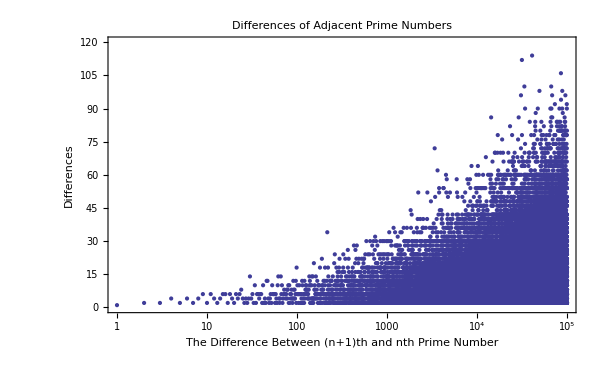

```mathematica
pltp=ListLogLinearPlot[p,AxesOrigin->{1,1},PlotRange->{Automatic,{0,120}},Frame->True,FrameLabel->{"The Difference Between (n+1)th and nth Prime Number","Differences"},PlotLabel->"Differences of Adjacent Prime Numbers",ImageSize->600]
```

```mathematica
Export["Export/PrimeNumbers1.png",pltp]
```

Export/PrimeNumbers1.png

```mathematica
p=Table[Prime[n],{n,1,10}]
```

{2,3,5,7,11,13,17,19,23,29}